# AntonAntonov/TileStats

Tilling over 2D data and related statistics

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Tilingstatistics.nb"DocumentationEnglishGuidesTilingstatistics.nb

"ReferencePages"

"Symbols"

"HextileBins.nb"DocumentationEnglishReferencePagesSymbolsHextileBins.nb

"HextileHistogram.nb"DocumentationEnglishReferencePagesSymbolsHextileHistogram.nb

"TileBins.nb"DocumentationEnglishReferencePagesSymbolsTileBins.nb

"TileBinsPlot.nb"DocumentationEnglishReferencePagesSymbolsTileBinsPlot.nb

"TileHistogram.nb"DocumentationEnglishReferencePagesSymbolsTileHistogram.nb

"Tutorials"

"Kernel"

"HextileBins.wl"KernelHextileBins.wl

"TileBins.wl"KernelTileBins.wl

"TileStats.wl"KernelTileStats.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

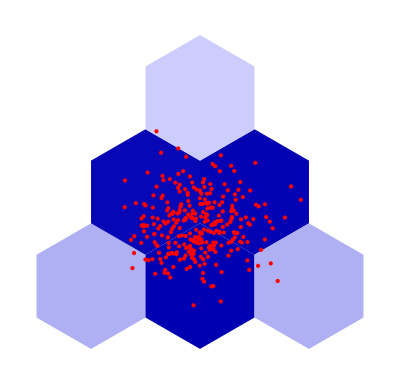

### Basic Description

Functions for hexagonal and rectangular tile binning of 2D data. Custom aggregation functions can be specified.

### Details

There two groups of functions: for binning and for 2D histogram plots.

The results of the binning functions are associations with keys that are polygon objects.

Tile histogram functions produce Graphics objects.

The option "AggregationFunction" is used to aggregate with different functions.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`TileStats`"];
```

### Basic Examples

Create a list of random 2D points:

```mathematica
SeedRandom[889];
data=RandomVariate[MultinormalDistribution[{10,10},7*IdentityMatrix[2]],300];
```

Bin the points:

```mathematica
HextileBins[data,10]
```

<|Polygon[…]→107,Polygon[…]→131,Polygon[…]→54,Polygon[…]→6,Polygon[…]→1,Polygon[…]→1|>

Show corresponding histogram (together with the points):

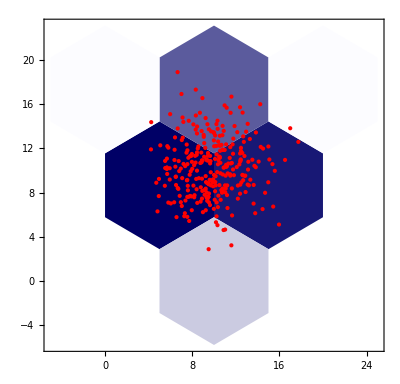

```mathematica
HextileHistogram[data,10,PlotRange->All,Epilog->{Red,Point[data]}]
```

Here is the corresponding rectangular histogram:

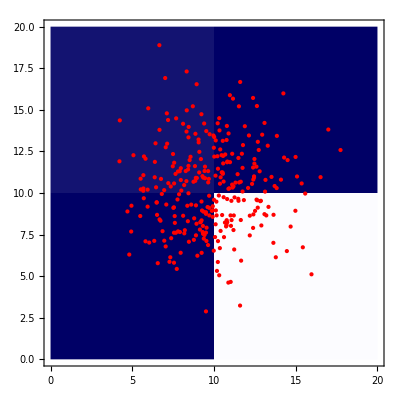

```mathematica
TileHistogram[data,10,PlotRange->All,Epilog->{Red,Point[data]}]
```

### Scope

Associate random values to 2D data:

```mathematica
SeedRandom[113];
data=RandomVariate[MultinormalDistribution[{10,10},7*IdentityMatrix[2]],200];dataRules=AssociationThread[data,RandomReal[{0,1},Length[data]]];
```

Bin the data rules:

```mathematica
HextileBins[dataRules,10]
```

<|Polygon[…]→46.9921,Polygon[…]→38.1256,Polygon[…]→15.3234,Polygon[…]→1.44698|>

Bin the keys of the data rules:

```mathematica
HextileBins[Keys@dataRules,10]
```

<|Polygon[…]→87,Polygon[…]→79,Polygon[…]→30,Polygon[…]→4|>

```mathematica
HextileBins[Keys@dataRules,10]==HextileBins[data,10]
```

True

Custom aggregation function can be specified for the binning process:

```mathematica
SeedRandom[113];
data3=RandomVariate[MultinormalDistribution[{10,10},{1,1.7}*IdentityMatrix[2]],300];dataRules3=AssociationThread[data3,RandomReal[{0,100},Length[data3]]];
```

```mathematica
res=HextileBins[dataRules3,10,"PolygonKeys"->False,"AggregationFunction"->ResourceFunction["RecordsSummary"]]
```

<|{5,5 √3}→{1 column 1
Min | 1.37421
1st Qu | 23.7983
Median | 45.6596
Mean | 47.4009
3rd Qu | 73.4392
Max | 99.9737},{15,5 √3}→{1 column 1
Min | 0.165429
1st Qu | 21.5524
Median | 43.7795
Mean | 47.1144
3rd Qu | 73.3877
Max | 99.4322},{10,10 √3}→{1 column 1
Min | 3.55093
1st Qu | 24.4037
Median | 36.0124
Mean | 48.9587
3rd Qu | 84.3097
Max | 95.4377}|>

Here is geographic data:

```mathematica
geoData=EntityValue[CountryData["Japan","LargestCities"],"Position"];
```

Here the corresponding geographic map and hexagonal histogram are plotted together:

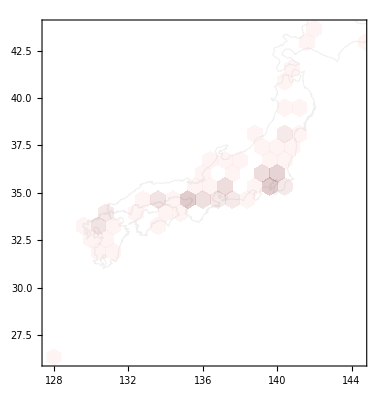

```mathematica
Show[GeoGraphics[{FaceForm[None],EdgeForm[GrayLevel[0.7]],Polygon[Entity["Country","Japan"]]},GeoProjection->"Equirectangular",GeoBackground->None],HextileHistogram[Reverse[#[[1]]]&/@geoData,0.8,ColorFunction->(Blend[{Lighter[Red,0.8],Darker[Red,0.6]},Sqrt[#]]&)]]
```

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-TileStats-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Binning

Bins

Hextile

Histogram

Tiling

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

HextileBins

HexagonalGridGraph

TileBins

### Original Source References and Attributions

Source, reference or citation

### Links

A monad for Epidemiologic Compartmental Modeling Workflows | Mathematica for prediction algorithms

### Compatibility

#### Wolfram Language Version

12.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.